```mathematica
gen5=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Length[FlatGenerators[allGraphs5[#,"colofour"]]]==1&];Length[gen5]
```

52

```mathematica
Table[allGraphs5[k,"graph"],{k,gen5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
prob=Table[Symbol["g"<>StringDrop[SymbolName[First[FlatGenerators[allGraphs5[k,"colofour"]]]],1]]==allGraphs5[k,"colofour"],{k,gen5}];
```

```mathematica
gen5Symbols=Sort[Table[Symbol["g"<>StringDrop[SymbolName[First[FlatGenerators[allGraphs5[k,"colofour"]]]],1]],{k,gen5}],CompareSymbols];
```

```mathematica
rep5=First[Solve[prob,Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]]];
```

```mathematica
gen5Coeff[form_]:=Table[Coefficient[form,term],{term, gen5Symbols}]
```

```mathematica
Monitor[Table [allGraphs5[k,"genfour"]=Simplify[allGraphs5[k,"colofour"]/.rep5],{k,Keys[allGraphs5]}],k]
```

{g12345,g1345x2+g134x25-g134x2x5+g135x24-g135x2x4+g13x245-g13x24x5-g13x25x4-g13x2x45+2 g13x2x4x5+g145x23-g145x2x3+g14x235-g14x23x5-g14x25x3-g14x2x35+2 g14x2x3x5+g15x234-g15x23x4-g15x24x3-g15x2x34+2 g15x2x3x4+g1x2345-g1x234x5-g1x235x4-g1x23x45+2 g1x23x4x5-g1x245x3-g1x24x35+2 g1x24x3x5-g1x25x34+2 g1x25x3x4-g1x2x345+2 g1x2x34x5+2 g1x2x35x4+2 g1x2x3x45-6 g1x2x3x4x5,1892,g12345-g1234x5-g1235x4+g123x4x5-g124x35+g124x3x5-g125x34+g125x3x4+g12x34x5+g12x35x4-2 g12x3x4x5-g134x25+g134x2x5-g135x24+g135x2x4+g13x24x5+g13x25x4-2 g13x2x4x5-g14x235+g14x23x5+g14x25x3+g14x2x35-2 g14x2x3x5-g15x234+g15x23x4+g15x24x3+g15x2x34-2 g15x2x3x4+g1x234x5+g1x235x4-2 g1x23x4x5+g1x24x35-2 g1x24x3x5+g1x25x34-2 g1x25x3x4-2 g1x2x34x5-2 g1x2x35x4+6 g1x2x3x4x5}
 |  |  |  |

```mathematica
fullSym=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols];
```

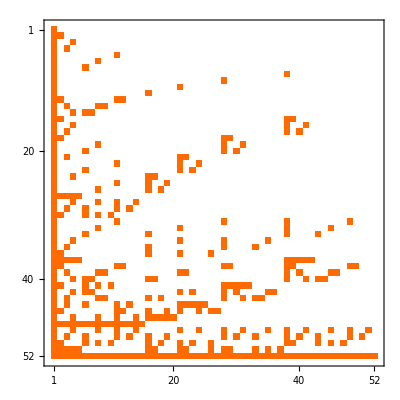

```mathematica
Table[gen5Coeff[allGraphs5[k,"colofour"]/.rep5//Simplify],{k,allGraphs5AtomKeys}]//Inverse//MatrixPlot
```

## Now with 6 nodes

```mathematica
gen6=Monitor[Select[Keys[allGraphs6],With[{k=#},VertexCount[allGraphs6[#,"graph"]]==6&&Length[FlatGenerators[allGraphs6[#,"colofour"]]]==1]&],k];Length[gen6]
```

203

```mathematica
Table[allGraphs6[k,"graph"],{k,gen6}]
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
prob=Table[Symbol["g"<>StringDrop[SymbolName[First[FlatGenerators[allGraphs6[k,"colofour"]]]],1]]==allGraphs6[k,"colofour"],{k,gen6}];
gen6Symbols=Sort[Table[Symbol["g"<>StringDrop[SymbolName[First[FlatGenerators[allGraphs6[k,"colofour"]]]],1]],{k,gen6}],CompareSymbols];
```

```mathematica
gen6Symbols
```

{g1x2x3x4x5x6,g1x2x3x4x56,g1x2x3x45x6,g1x2x3x46x5,g1x2x34x5x6,g1x2x35x4x6,g1x2x36x4x5,g1x23x4x5x6,g1x24x3x5x6,g1x25x3x4x6,g1x26x3x4x5,g12x3x4x5x6,g13x2x4x5x6,g14x2x3x5x6,g15x2x3x4x6,g16x2x3x4x5,g1x2x34x56,g1x2x35x46,g1x2x36x45,g1x23x4x56,g1x23x45x6,g1x23x46x5,g1x24x3x56,g1x24x35x6,g1x24x36x5,g1x25x3x46,g1x25x34x6,g1x25x36x4,g1x26x3x45,g1x26x34x5,g1x26x35x4,g12x3x4x56,g12x3x45x6,g12x3x46x5,g12x34x5x6,g12x35x4x6,g12x36x4x5,g13x2x4x56,g13x2x45x6,g13x2x46x5,g13x24x5x6,g13x25x4x6,g13x26x4x5,g14x2x3x56,g14x2x35x6,g14x2x36x5,g14x23x5x6,g14x25x3x6,g14x26x3x5,g15x2x3x46,g15x2x34x6,g15x2x36x4,g15x23x4x6,g15x24x3x6,g15x26x3x4,g16x2x3x45,g16x2x34x5,g16x2x35x4,g16x23x4x5,g16x24x3x5,g16x25x3x4,g1x2x3x456,g1x2x345x6,g1x2x346x5,g1x2x356x4,g1x234x5x6,g1x235x4x6,g1x236x4x5,g1x245x3x6,g1x246x3x5,g1x256x3x4,g123x4x5x6,g124x3x5x6,g125x3x4x6,g126x3x4x5,g134x2x5x6,g135x2x4x6,g136x2x4x5,g145x2x3x6,g146x2x3x5,g156x2x3x4,g12x34x56,g12x35x46,g12x36x45,g13x24x56,g13x25x46,g13x26x45,g14x23x56,g14x25x36,g14x26x35,g15x23x46,g15x24x36,g15x26x34,g16x23x45,g16x24x35,g16x25x34,g1x23x456,g1x234x56,g1x235x46,g1x236x45,g1x24x356,g1x245x36,g1x246x35,g1x25x346,g1x256x34,g1x26x345,g12x3x456,g12x345x6,g12x346x5,g12x356x4,g123x4x56,g123x45x6,g123x46x5,g124x3x56,g124x35x6,g124x36x5,g125x3x46,g125x34x6,g125x36x4,g126x3x45,g126x34x5,g126x35x4,g13x2x456,g13x245x6,g13x246x5,g13x256x4,g134x2x56,g134x25x6,g134x26x5,g135x2x46,g135x24x6,g135x26x4,g136x2x45,g136x24x5,g136x25x4,g14x2x356,g14x235x6,g14x236x5,g14x256x3,g145x2x36,g145x23x6,g145x26x3,g146x2x35,g146x23x5,g146x25x3,g15x2x346,g15x234x6,g15x236x4,g15x246x3,g156x2x34,g156x23x4,g156x24x3,g16x2x345,g16x234x5,g16x235x4,g16x245x3,g1x2x3456,g1x2345x6,g1x2346x5,g1x2356x4,g1x2456x3,g1234x5x6,g1235x4x6,g1236x4x5,g1245x3x6,g1246x3x5,g1256x3x4,g1345x2x6,g1346x2x5,g1356x2x4,g1456x2x3,g123x456,g124x356,g125x346,g126x345,g134x256,g135x246,g136x245,g145x236,g146x235,g156x234,g12x3456,g1234x56,g1235x46,g1236x45,g1245x36,g1246x35,g1256x34,g13x2456,g1345x26,g1346x25,g1356x24,g14x2356,g1456x23,g15x2346,g16x2345,g1x23456,g12345x6,g12346x5,g12356x4,g12456x3,g13456x2,g123456}

```mathematica
rep6=First[Solve[prob,Table[allGraphs6[k,"colofour"],{k,allGraphs6AtomKeys}]]];
gen6Coeff[form_]:=Table[Coefficient[form,term],{term, gen6Symbols}]
fullSym=Sort[Table[allGraphs6[k,"colofour"],{k,allGraphs6AtomKeys}],CompareSymbols];
```

```mathematica
Clear[k]
```

```mathematica
Monitor[Table [allGraphs6[k,"genfour"]=Simplify[allGraphs6[k,"colofour"]/.rep6],{k,Keys[allGraphs6]}],k];
```

```mathematica
full6Coeff[form_]:=Table[Coefficient[form,term],{term, fullSym}]
```

```mathematica
fullSym5=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x45,v1x24x35,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v13x2x45,v13x24x5,v13x25x4,v14x2x35,v14x23x5,v14x25x3,v15x2x34,v15x23x4,v15x24x3,v1x2x345,v1x234x5,v1x235x4,v1x245x3,v123x4x5,v124x3x5,v125x3x4,v134x2x5,v135x2x4,v145x2x3,v12x345,v123x45,v124x35,v125x34,v13x245,v134x25,v135x24,v14x235,v145x23,v15x234,v1x2345,v1234x5,v1235x4,v1245x3,v1345x2,v12345}

```mathematica
full5Coeff[form_]:=Table[Coefficient[form,term],{term, fullSym5}]
```

```mathematica
gen6Sorted=Sort[gen6,CompareSymbols[allGraphs6[#1,"genfour"],allGraphs6[#2,"genfour"]]&]
```

{7174453,7174452,7174444,7174450,7174210,7174372,7174426,7154770,7167892,7172266,7173724,2391484,5580130,6643012,6997306,7115404,7174209,7174369,7174417,7154769,7154761,7154767,7167891,7167811,7167865,7172263,7172023,7172239,7173715,7173481,7173643,2391483,2391475,2391481,2391241,2391403,2391457,5580129,5580121,5580127,5573569,5577943,5579401,6643011,6642931,6642985,6623329,6640825,6642283,6997303,6997063,6997279,6977623,6990745,6996577,7115395,7115161,7115323,7095721,7108843,7113217,7174440,7174120,7174180,7174344,7147966,7152502,7154014,7165696,7167160,7171536,777478,1853482,2212150,2331706,5048446,5402902,5521054,6465856,6583960,6938256,2391240,2391400,2391448,5573568,5577940,5579392,6623328,6640798,6642202,6977620,6990718,6996334,7095712,7108762,7112974,7154757,7147965,7152499,7154005,7167783,7165669,7167079,7171993,7171293,7173391,2391471,2391151,2391211,2391375,777477,777469,777475,1853481,1853401,1853455,2212147,2211907,2212123,2331697,2331463,2331625,5580117,5571373,5572837,5577213,5048445,5046259,5047717,5402899,5396341,5402173,5521045,5514493,5518867,6642903,6621061,6622573,6640095,6465829,6446173,6465127,6583879,6564277,6581773,6997033,6970819,6976867,6990013,6938013,6918573,6931695,7115071,7088917,7093453,7106647,7174089,7145689,7147207,7151745,7164963,239233,598063,717673,1674139,1793701,2152371,4871209,4989367,5343825,6406803,777465,1853373,2211877,2331373,5045529,5395609,5512297,6445417,6562009,6911769,2391120,239232,598060,717664,1674112,1793620,2152128,5570640,4870480,4987180,5337264,6620304,6387120,6970060,7086640,7144929,59809,179425,538257,1614357,4812129,0}

```mathematica
gen5Sorted=Sort[gen5,CompareSymbols[allGraphs5[#1,"genfour"],allGraphs5[#2,"genfour"]]&]
```

{29524,29523,29515,29521,29281,29443,29497,9841,22963,27337,28795,29280,29440,29488,9840,9832,9838,22962,22882,22936,27334,27094,27310,28786,28552,28714,29511,29191,29251,29415,3037,7573,9085,20767,22231,26607,9828,3036,7570,9076,22854,20740,22150,27064,26364,28462,29160,760,2278,6816,20034,0}

```mathematica
fullSorted=Sort[allGraphs6AtomKeys,CompareSymbols[allGraphs6[#1,"colofour"],allGraphs6[#2,"colofour"]]&]
```

{7174453,7174454,7174462,7174456,7174696,7174534,7174480,7194136,7181014,7176640,7175182,11957422,8768776,7705894,7351600,7233502,7174697,7174537,7174489,7194137,7194145,7194139,7181015,7181095,7181041,7176643,7176883,7176667,7175191,7175425,7175263,11957423,11957431,11957425,11957665,11957503,11957449,8768777,8768785,8768779,8775337,8770963,8769505,7705895,7705975,7705921,7725577,7708081,7706623,7351603,7351843,7351627,7371283,7358161,7352329,7233511,7233745,7233583,7253185,7240063,7235689,7174466,7174786,7174726,7174562,7200940,7196404,7194892,7183210,7181746,7177370,13571428,12495424,12136756,12017200,9300460,8946004,8827852,7883050,7764946,7410650,11957666,11957506,11957458,8775338,8770966,8769514,7725578,7708108,7706704,7371286,7358188,7352572,7253194,7240144,7235932,7194149,7200941,7196407,7194901,7181123,7183237,7181827,7176913,7177613,7175515,11957435,11957755,11957695,11957531,13571429,13571437,13571431,12495425,12495505,12495451,12136759,12136999,12136783,12017209,12017443,12017281,8768789,8777533,8776069,8771693,9300461,9302647,9301189,8946007,8952565,8946733,8827861,8834413,8830039,7706003,7727845,7726333,7708811,7883077,7902733,7883779,7765027,7784629,7767133,7351873,7378087,7372039,7358893,7410893,7430333,7417211,7233835,7259989,7255453,7242259,7174817,7203217,7201699,7197161,7183943,14109673,13750843,13631233,12674767,12555205,12196535,9477697,9359539,9005081,7942103,13571441,12495533,12137029,12017533,9303377,8953297,8836609,7903489,7786897,7437137,11957786,14109674,13750846,13631242,12674794,12555286,12196778,8778266,9478426,9361726,9011642,7728602,7961786,7378846,7262266,7203977,14289097,14169481,13810649,12734549,9536777,14348906}

```mathematica
Intersection[gen6Sorted,fullSorted]
```

{7174453}

```mathematica
allGraphs6[7174453,"graph"]
```

-Graphics-

```mathematica
{L,U,c}=LUDecomposition[ Table[gen6Coeff[allGraphs6[k,"genfour"]],{k,allGraphs6AtomKeys}]]
```

{1}
 |  |  |  |

```mathematica
OneZero[mat_]:=Map[Map[If[#==0,0,1]&,#]&,mat]
```

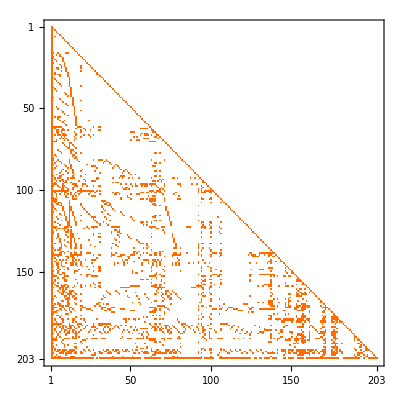

```mathematica
MatrixPlot[OneZero[LowerTriangularize[L]]]
```

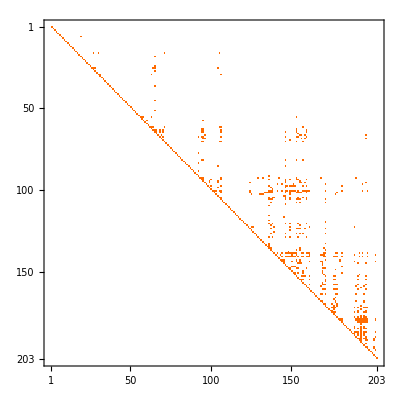

```mathematica
MatrixPlot[OneZero[UpperTriangularize[L]]]
```

```mathematica
Table[allGraphs6[k,"genfour"],{k,allGraphs6AtomKeys}]
```

{g1x2x3x4x5x6,g1x2x3x4x56-g1x2x3x4x5x6,g1x2x3x46x5-g1x2x3x4x5x6,g1x2x3x45x6-g1x2x3x4x5x6,g1x2x3x456-g1x2x3x45x6-g1x2x3x46x5-g1x2x3x4x56+2 g1x2x3x4x5x6,g1x2x36x4x5-g1x2x3x4x5x6,g1x2x36x45-g1x2x36x4x5-g1x2x3x45x6+g1x2x3x4x5x6,g1x2x35x4x6-g1x2x3x4x5x6,g1x2x35x46-g1x2x35x4x6-g1x2x3x46x5+g1x2x3x4x5x6,g1x2x356x4-g1x2x35x4x6-g1x2x36x4x5-g1x2x3x4x56+2 g1x2x3x4x5x6,g1x2x34x5x6-g1x2x3x4x5x6,g1x2x34x56-g1x2x34x5x6-g1x2x3x4x56+g1x2x3x4x5x6,g1x2x346x5-g1x2x34x5x6-g1x2x36x4x5-g1x2x3x46x5+2 g1x2x3x4x5x6,g1x2x345x6-g1x2x34x5x6-g1x2x35x4x6-g1x2x3x45x6+2 g1x2x3x4x5x6,g1x2x3456-g1x2x345x6-g1x2x346x5-g1x2x34x56+2 g1x2x34x5x6-g1x2x356x4-g1x2x35x46+2 g1x2x35x4x6-g1x2x36x45+2 g1x2x36x4x5-g1x2x3x456+2 g1x2x3x45x6+2 g1x2x3x46x5+2 g1x2x3x4x56-6 g1x2x3x4x5x6,g1x26x3x4x5-g1x2x3x4x5x6,g1x26x3x45-g1x26x3x4x5-g1x2x3x45x6+g1x2x3x4x5x6,g1x26x35x4-g1x26x3x4x5-g1x2x35x4x6+g1x2x3x4x5x6,g1x26x34x5-g1x26x3x4x5-g1x2x34x5x6+g1x2x3x4x5x6,g1x26x345-g1x26x34x5-g1x26x35x4-g1x26x3x45+2 g1x26x3x4x5-g1x2x345x6+g1x2x34x5x6+g1x2x35x4x6+g1x2x3x45x6-2 g1x2x3x4x5x6,g1x25x3x4x6-g1x2x3x4x5x6,g1x25x3x46-g1x25x3x4x6-g1x2x3x46x5+g1x2x3x4x5x6,g1x25x36x4-g1x25x3x4x6-g1x2x36x4x5+g1x2x3x4x5x6,g1x25x34x6-g1x25x3x4x6-g1x2x34x5x6+g1x2x3x4x5x6,g1x25x346-g1x25x34x6-g1x25x36x4-g1x25x3x46+2 g1x25x3x4x6-g1x2x346x5+g1x2x34x5x6+g1x2x36x4x5+g1x2x3x46x5-2 g1x2x3x4x5x6,g1x256x3x4-g1x25x3x4x6-g1x26x3x4x5-g1x2x3x4x56+2 g1x2x3x4x5x6,g1x256x34-g1x256x3x4-g1x25x34x6+g1x25x3x4x6-g1x26x34x5+g1x26x3x4x5-g1x2x34x56+2 g1x2x34x5x6+g1x2x3x4x56-2 g1x2x3x4x5x6,g1x24x3x5x6-g1x2x3x4x5x6,g1x24x3x56-g1x24x3x5x6-g1x2x3x4x56+g1x2x3x4x5x6,g1x24x36x5-g1x24x3x5x6-g1x2x36x4x5+g1x2x3x4x5x6,g1x24x35x6-g1x24x3x5x6-g1x2x35x4x6+g1x2x3x4x5x6,g1x24x356-g1x24x35x6-g1x24x36x5-g1x24x3x56+2 g1x24x3x5x6-g1x2x356x4+g1x2x35x4x6+g1x2x36x4x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g1x246x3x5-g1x24x3x5x6-g1x26x3x4x5-g1x2x3x46x5+2 g1x2x3x4x5x6,g1x246x35-g1x246x3x5-g1x24x35x6+g1x24x3x5x6-g1x26x35x4+g1x26x3x4x5-g1x2x35x46+2 g1x2x35x4x6+g1x2x3x46x5-2 g1x2x3x4x5x6,g1x245x3x6-g1x24x3x5x6-g1x25x3x4x6-g1x2x3x45x6+2 g1x2x3x4x5x6,g1x245x36-g1x245x3x6-g1x24x36x5+g1x24x3x5x6-g1x25x36x4+g1x25x3x4x6-g1x2x36x45+2 g1x2x36x4x5+g1x2x3x45x6-2 g1x2x3x4x5x6,g1x2456x3-g1x245x3x6-g1x246x3x5-g1x24x3x56+2 g1x24x3x5x6-g1x256x3x4-g1x25x3x46+2 g1x25x3x4x6-g1x26x3x45+2 g1x26x3x4x5-g1x2x3x456+2 g1x2x3x45x6+2 g1x2x3x46x5+2 g1x2x3x4x56-6 g1x2x3x4x5x6,g1x23x4x5x6-g1x2x3x4x5x6,g1x23x4x56-g1x23x4x5x6-g1x2x3x4x56+g1x2x3x4x5x6,g1x23x46x5-g1x23x4x5x6-g1x2x3x46x5+g1x2x3x4x5x6,g1x23x45x6-g1x23x4x5x6-g1x2x3x45x6+g1x2x3x4x5x6,g1x23x456-g1x23x45x6-g1x23x46x5-g1x23x4x56+2 g1x23x4x5x6-g1x2x3x456+g1x2x3x45x6+g1x2x3x46x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g1x236x4x5-g1x23x4x5x6-g1x26x3x4x5-g1x2x36x4x5+2 g1x2x3x4x5x6,g1x236x45-g1x236x4x5-g1x23x45x6+g1x23x4x5x6-g1x26x3x45+g1x26x3x4x5-g1x2x36x45+g1x2x36x4x5+2 g1x2x3x45x6-2 g1x2x3x4x5x6,g1x235x4x6-g1x23x4x5x6-g1x25x3x4x6-g1x2x35x4x6+2 g1x2x3x4x5x6,g1x235x46-g1x235x4x6-g1x23x46x5+g1x23x4x5x6-g1x25x3x46+g1x25x3x4x6-g1x2x35x46+g1x2x35x4x6+2 g1x2x3x46x5-2 g1x2x3x4x5x6,g1x2356x4-g1x235x4x6-g1x236x4x5-g1x23x4x56+2 g1x23x4x5x6-g1x256x3x4-g1x25x36x4+2 g1x25x3x4x6-g1x26x35x4+2 g1x26x3x4x5-g1x2x356x4+2 g1x2x35x4x6+2 g1x2x36x4x5+2 g1x2x3x4x56-6 g1x2x3x4x5x6,g1x234x5x6-g1x23x4x5x6-g1x24x3x5x6-g1x2x34x5x6+2 g1x2x3x4x5x6,g1x234x56-g1x234x5x6-g1x23x4x56+g1x23x4x5x6-g1x24x3x56+g1x24x3x5x6-g1x2x34x56+g1x2x34x5x6+2 g1x2x3x4x56-2 g1x2x3x4x5x6,g1x2346x5-g1x234x5x6-g1x236x4x5-g1x23x46x5+2 g1x23x4x5x6-g1x246x3x5-g1x24x36x5+2 g1x24x3x5x6-g1x26x34x5+2 g1x26x3x4x5-g1x2x346x5+2 g1x2x34x5x6+2 g1x2x36x4x5+2 g1x2x3x46x5-6 g1x2x3x4x5x6,g1x2345x6-g1x234x5x6-g1x235x4x6-g1x23x45x6+2 g1x23x4x5x6-g1x245x3x6-g1x24x35x6+2 g1x24x3x5x6-g1x25x34x6+2 g1x25x3x4x6-g1x2x345x6+2 g1x2x34x5x6+2 g1x2x35x4x6+2 g1x2x3x45x6-6 g1x2x3x4x5x6,g1x23456-g1x2345x6-g1x2346x5-g1x234x56+2 g1x234x5x6-g1x2356x4-g1x235x46+2 g1x235x4x6-g1x236x45+2 g1x236x4x5-g1x23x456+2 g1x23x45x6+2 g1x23x46x5+2 g1x23x4x56-6 g1x23x4x5x6-g1x2456x3-g1x245x36+2 g1x245x3x6-g1x246x35+2 g1x246x3x5-g1x24x356+2 g1x24x35x6+2 g1x24x36x5+2 g1x24x3x56-6 g1x24x3x5x6-g1x256x34+2 g1x256x3x4-g1x25x346+2 g1x25x34x6+2 g1x25x36x4+2 g1x25x3x46-6 g1x25x3x4x6-g1x26x345+2 g1x26x34x5+2 g1x26x35x4+2 g1x26x3x45-6 g1x26x3x4x5-g1x2x3456+2 g1x2x345x6+2 g1x2x346x5+2 g1x2x34x56-6 g1x2x34x5x6+2 g1x2x356x4+2 g1x2x35x46-6 g1x2x35x4x6+2 g1x2x36x45-6 g1x2x36x4x5+2 g1x2x3x456-6 g1x2x3x45x6-6 g1x2x3x46x5-6 g1x2x3x4x56+24 g1x2x3x4x5x6,g16x2x3x4x5-g1x2x3x4x5x6,g16x2x3x45-g16x2x3x4x5-g1x2x3x45x6+g1x2x3x4x5x6,g16x2x35x4-g16x2x3x4x5-g1x2x35x4x6+g1x2x3x4x5x6,g16x2x34x5-g16x2x3x4x5-g1x2x34x5x6+g1x2x3x4x5x6,g16x2x345-g16x2x34x5-g16x2x35x4-g16x2x3x45+2 g16x2x3x4x5-g1x2x345x6+g1x2x34x5x6+g1x2x35x4x6+g1x2x3x45x6-2 g1x2x3x4x5x6,g16x25x3x4-g16x2x3x4x5-g1x25x3x4x6+g1x2x3x4x5x6,g16x25x34-g16x25x3x4-g16x2x34x5+g16x2x3x4x5-g1x25x34x6+g1x25x3x4x6+g1x2x34x5x6-g1x2x3x4x5x6,g16x24x3x5-g16x2x3x4x5-g1x24x3x5x6+g1x2x3x4x5x6,g16x24x35-g16x24x3x5-g16x2x35x4+g16x2x3x4x5-g1x24x35x6+g1x24x3x5x6+g1x2x35x4x6-g1x2x3x4x5x6,g16x245x3-g16x24x3x5-g16x25x3x4-g16x2x3x45+2 g16x2x3x4x5-g1x245x3x6+g1x24x3x5x6+g1x25x3x4x6+g1x2x3x45x6-2 g1x2x3x4x5x6,g16x23x4x5-g16x2x3x4x5-g1x23x4x5x6+g1x2x3x4x5x6,g16x23x45-g16x23x4x5-g16x2x3x45+g16x2x3x4x5-g1x23x45x6+g1x23x4x5x6+g1x2x3x45x6-g1x2x3x4x5x6,g16x235x4-g16x23x4x5-g16x25x3x4-g16x2x35x4+2 g16x2x3x4x5-g1x235x4x6+g1x23x4x5x6+g1x25x3x4x6+g1x2x35x4x6-2 g1x2x3x4x5x6,g16x234x5-g16x23x4x5-g16x24x3x5-g16x2x34x5+2 g16x2x3x4x5-g1x234x5x6+g1x23x4x5x6+g1x24x3x5x6+g1x2x34x5x6-2 g1x2x3x4x5x6,g16x2345-g16x234x5-g16x235x4-g16x23x45+2 g16x23x4x5-g16x245x3-g16x24x35+2 g16x24x3x5-g16x25x34+2 g16x25x3x4-g16x2x345+2 g16x2x34x5+2 g16x2x35x4+2 g16x2x3x45-6 g16x2x3x4x5-g1x2345x6+g1x234x5x6+g1x235x4x6+g1x23x45x6-2 g1x23x4x5x6+g1x245x3x6+g1x24x35x6-2 g1x24x3x5x6+g1x25x34x6-2 g1x25x3x4x6+g1x2x345x6-2 g1x2x34x5x6-2 g1x2x35x4x6-2 g1x2x3x45x6+6 g1x2x3x4x5x6,g15x2x3x4x6-g1x2x3x4x5x6,g15x2x3x46-g15x2x3x4x6-g1x2x3x46x5+g1x2x3x4x5x6,g15x2x36x4-g15x2x3x4x6-g1x2x36x4x5+g1x2x3x4x5x6,g15x2x34x6-g15x2x3x4x6-g1x2x34x5x6+g1x2x3x4x5x6,g15x2x346-g15x2x34x6-g15x2x36x4-g15x2x3x46+2 g15x2x3x4x6-g1x2x346x5+g1x2x34x5x6+g1x2x36x4x5+g1x2x3x46x5-2 g1x2x3x4x5x6,g15x26x3x4-g15x2x3x4x6-g1x26x3x4x5+g1x2x3x4x5x6,g15x26x34-g15x26x3x4-g15x2x34x6+g15x2x3x4x6-g1x26x34x5+g1x26x3x4x5+g1x2x34x5x6-g1x2x3x4x5x6,g15x24x3x6-g15x2x3x4x6-g1x24x3x5x6+g1x2x3x4x5x6,g15x24x36-g15x24x3x6-g15x2x36x4+g15x2x3x4x6-g1x24x36x5+g1x24x3x5x6+g1x2x36x4x5-g1x2x3x4x5x6,g15x246x3-g15x24x3x6-g15x26x3x4-g15x2x3x46+2 g15x2x3x4x6-g1x246x3x5+g1x24x3x5x6+g1x26x3x4x5+g1x2x3x46x5-2 g1x2x3x4x5x6,g15x23x4x6-g15x2x3x4x6-g1x23x4x5x6+g1x2x3x4x5x6,g15x23x46-g15x23x4x6-g15x2x3x46+g15x2x3x4x6-g1x23x46x5+g1x23x4x5x6+g1x2x3x46x5-g1x2x3x4x5x6,g15x236x4-g15x23x4x6-g15x26x3x4-g15x2x36x4+2 g15x2x3x4x6-g1x236x4x5+g1x23x4x5x6+g1x26x3x4x5+g1x2x36x4x5-2 g1x2x3x4x5x6,g15x234x6-g15x23x4x6-g15x24x3x6-g15x2x34x6+2 g15x2x3x4x6-g1x234x5x6+g1x23x4x5x6+g1x24x3x5x6+g1x2x34x5x6-2 g1x2x3x4x5x6,g15x2346-g15x234x6-g15x236x4-g15x23x46+2 g15x23x4x6-g15x246x3-g15x24x36+2 g15x24x3x6-g15x26x34+2 g15x26x3x4-g15x2x346+2 g15x2x34x6+2 g15x2x36x4+2 g15x2x3x46-6 g15x2x3x4x6-g1x2346x5+g1x234x5x6+g1x236x4x5+g1x23x46x5-2 g1x23x4x5x6+g1x246x3x5+g1x24x36x5-2 g1x24x3x5x6+g1x26x34x5-2 g1x26x3x4x5+g1x2x346x5-2 g1x2x34x5x6-2 g1x2x36x4x5-2 g1x2x3x46x5+6 g1x2x3x4x5x6,g156x2x3x4-g15x2x3x4x6-g16x2x3x4x5-g1x2x3x4x56+2 g1x2x3x4x5x6,g156x2x34-g156x2x3x4-g15x2x34x6+g15x2x3x4x6-g16x2x34x5+g16x2x3x4x5-g1x2x34x56+2 g1x2x34x5x6+g1x2x3x4x56-2 g1x2x3x4x5x6,g156x24x3-g156x2x3x4-g15x24x3x6+g15x2x3x4x6-g16x24x3x5+g16x2x3x4x5-g1x24x3x56+2 g1x24x3x5x6+g1x2x3x4x56-2 g1x2x3x4x5x6,g156x23x4-g156x2x3x4-g15x23x4x6+g15x2x3x4x6-g16x23x4x5+g16x2x3x4x5-g1x23x4x56+2 g1x23x4x5x6+g1x2x3x4x56-2 g1x2x3x4x5x6,g156x234-g156x23x4-g156x24x3-g156x2x34+2 g156x2x3x4-g15x234x6+g15x23x4x6+g15x24x3x6+g15x2x34x6-2 g15x2x3x4x6-g16x234x5+g16x23x4x5+g16x24x3x5+g16x2x34x5-2 g16x2x3x4x5-g1x234x56+2 g1x234x5x6+g1x23x4x56-2 g1x23x4x5x6+g1x24x3x56-2 g1x24x3x5x6+g1x2x34x56-2 g1x2x34x5x6-2 g1x2x3x4x56+4 g1x2x3x4x5x6,g14x2x3x5x6-g1x2x3x4x5x6,g14x2x3x56-g14x2x3x5x6-g1x2x3x4x56+g1x2x3x4x5x6,g14x2x36x5-g14x2x3x5x6-g1x2x36x4x5+g1x2x3x4x5x6,g14x2x35x6-g14x2x3x5x6-g1x2x35x4x6+g1x2x3x4x5x6,g14x2x356-g14x2x35x6-g14x2x36x5-g14x2x3x56+2 g14x2x3x5x6-g1x2x356x4+g1x2x35x4x6+g1x2x36x4x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g14x26x3x5-g14x2x3x5x6-g1x26x3x4x5+g1x2x3x4x5x6,g14x26x35-g14x26x3x5-g14x2x35x6+g14x2x3x5x6-g1x26x35x4+g1x26x3x4x5+g1x2x35x4x6-g1x2x3x4x5x6,g14x25x3x6-g14x2x3x5x6-g1x25x3x4x6+g1x2x3x4x5x6,g14x25x36-g14x25x3x6-g14x2x36x5+g14x2x3x5x6-g1x25x36x4+g1x25x3x4x6+g1x2x36x4x5-g1x2x3x4x5x6,g14x256x3-g14x25x3x6-g14x26x3x5-g14x2x3x56+2 g14x2x3x5x6-g1x256x3x4+g1x25x3x4x6+g1x26x3x4x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g14x23x5x6-g14x2x3x5x6-g1x23x4x5x6+g1x2x3x4x5x6,g14x23x56-g14x23x5x6-g14x2x3x56+g14x2x3x5x6-g1x23x4x56+g1x23x4x5x6+g1x2x3x4x56-g1x2x3x4x5x6,g14x236x5-g14x23x5x6-g14x26x3x5-g14x2x36x5+2 g14x2x3x5x6-g1x236x4x5+g1x23x4x5x6+g1x26x3x4x5+g1x2x36x4x5-2 g1x2x3x4x5x6,g14x235x6-g14x23x5x6-g14x25x3x6-g14x2x35x6+2 g14x2x3x5x6-g1x235x4x6+g1x23x4x5x6+g1x25x3x4x6+g1x2x35x4x6-2 g1x2x3x4x5x6,g14x2356-g14x235x6-g14x236x5-g14x23x56+2 g14x23x5x6-g14x256x3-g14x25x36+2 g14x25x3x6-g14x26x35+2 g14x26x3x5-g14x2x356+2 g14x2x35x6+2 g14x2x36x5+2 g14x2x3x56-6 g14x2x3x5x6-g1x2356x4+g1x235x4x6+g1x236x4x5+g1x23x4x56-2 g1x23x4x5x6+g1x256x3x4+g1x25x36x4-2 g1x25x3x4x6+g1x26x35x4-2 g1x26x3x4x5+g1x2x356x4-2 g1x2x35x4x6-2 g1x2x36x4x5-2 g1x2x3x4x56+6 g1x2x3x4x5x6,g146x2x3x5-g14x2x3x5x6-g16x2x3x4x5-g1x2x3x46x5+2 g1x2x3x4x5x6,g146x2x35-g146x2x3x5-g14x2x35x6+g14x2x3x5x6-g16x2x35x4+g16x2x3x4x5-g1x2x35x46+2 g1x2x35x4x6+g1x2x3x46x5-2 g1x2x3x4x5x6,g146x25x3-g146x2x3x5-g14x25x3x6+g14x2x3x5x6-g16x25x3x4+g16x2x3x4x5-g1x25x3x46+2 g1x25x3x4x6+g1x2x3x46x5-2 g1x2x3x4x5x6,g146x23x5-g146x2x3x5-g14x23x5x6+g14x2x3x5x6-g16x23x4x5+g16x2x3x4x5-g1x23x46x5+2 g1x23x4x5x6+g1x2x3x46x5-2 g1x2x3x4x5x6,g146x235-g146x23x5-g146x25x3-g146x2x35+2 g146x2x3x5-g14x235x6+g14x23x5x6+g14x25x3x6+g14x2x35x6-2 g14x2x3x5x6-g16x235x4+g16x23x4x5+g16x25x3x4+g16x2x35x4-2 g16x2x3x4x5-g1x235x46+2 g1x235x4x6+g1x23x46x5-2 g1x23x4x5x6+g1x25x3x46-2 g1x25x3x4x6+g1x2x35x46-2 g1x2x35x4x6-2 g1x2x3x46x5+4 g1x2x3x4x5x6,g145x2x3x6-g14x2x3x5x6-g15x2x3x4x6-g1x2x3x45x6+2 g1x2x3x4x5x6,g145x2x36-g145x2x3x6-g14x2x36x5+g14x2x3x5x6-g15x2x36x4+g15x2x3x4x6-g1x2x36x45+2 g1x2x36x4x5+g1x2x3x45x6-2 g1x2x3x4x5x6,g145x26x3-g145x2x3x6-g14x26x3x5+g14x2x3x5x6-g15x26x3x4+g15x2x3x4x6-g1x26x3x45+2 g1x26x3x4x5+g1x2x3x45x6-2 g1x2x3x4x5x6,g145x23x6-g145x2x3x6-g14x23x5x6+g14x2x3x5x6-g15x23x4x6+g15x2x3x4x6-g1x23x45x6+2 g1x23x4x5x6+g1x2x3x45x6-2 g1x2x3x4x5x6,g145x236-g145x23x6-g145x26x3-g145x2x36+2 g145x2x3x6-g14x236x5+g14x23x5x6+g14x26x3x5+g14x2x36x5-2 g14x2x3x5x6-g15x236x4+g15x23x4x6+g15x26x3x4+g15x2x36x4-2 g15x2x3x4x6-g1x236x45+2 g1x236x4x5+g1x23x45x6-2 g1x23x4x5x6+g1x26x3x45-2 g1x26x3x4x5+g1x2x36x45-2 g1x2x36x4x5-2 g1x2x3x45x6+4 g1x2x3x4x5x6,g1456x2x3-g145x2x3x6-g146x2x3x5-g14x2x3x56+2 g14x2x3x5x6-g156x2x3x4-g15x2x3x46+2 g15x2x3x4x6-g16x2x3x45+2 g16x2x3x4x5-g1x2x3x456+2 g1x2x3x45x6+2 g1x2x3x46x5+2 g1x2x3x4x56-6 g1x2x3x4x5x6,g1456x23-g1456x2x3-g145x23x6+g145x2x3x6-g146x23x5+g146x2x3x5-g14x23x56+2 g14x23x5x6+g14x2x3x56-2 g14x2x3x5x6-g156x23x4+g156x2x3x4-g15x23x46+2 g15x23x4x6+g15x2x3x46-2 g15x2x3x4x6-g16x23x45+2 g16x23x4x5+g16x2x3x45-2 g16x2x3x4x5-g1x23x456+2 g1x23x45x6+2 g1x23x46x5+2 g1x23x4x56-6 g1x23x4x5x6+g1x2x3x456-2 g1x2x3x45x6-2 g1x2x3x46x5-2 g1x2x3x4x56+6 g1x2x3x4x5x6,g13x2x4x5x6-g1x2x3x4x5x6,g13x2x4x56-g13x2x4x5x6-g1x2x3x4x56+g1x2x3x4x5x6,g13x2x46x5-g13x2x4x5x6-g1x2x3x46x5+g1x2x3x4x5x6,g13x2x45x6-g13x2x4x5x6-g1x2x3x45x6+g1x2x3x4x5x6,g13x2x456-g13x2x45x6-g13x2x46x5-g13x2x4x56+2 g13x2x4x5x6-g1x2x3x456+g1x2x3x45x6+g1x2x3x46x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g13x26x4x5-g13x2x4x5x6-g1x26x3x4x5+g1x2x3x4x5x6,g13x26x45-g13x26x4x5-g13x2x45x6+g13x2x4x5x6-g1x26x3x45+g1x26x3x4x5+g1x2x3x45x6-g1x2x3x4x5x6,g13x25x4x6-g13x2x4x5x6-g1x25x3x4x6+g1x2x3x4x5x6,g13x25x46-g13x25x4x6-g13x2x46x5+g13x2x4x5x6-g1x25x3x46+g1x25x3x4x6+g1x2x3x46x5-g1x2x3x4x5x6,g13x256x4-g13x25x4x6-g13x26x4x5-g13x2x4x56+2 g13x2x4x5x6-g1x256x3x4+g1x25x3x4x6+g1x26x3x4x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g13x24x5x6-g13x2x4x5x6-g1x24x3x5x6+g1x2x3x4x5x6,g13x24x56-g13x24x5x6-g13x2x4x56+g13x2x4x5x6-g1x24x3x56+g1x24x3x5x6+g1x2x3x4x56-g1x2x3x4x5x6,g13x246x5-g13x24x5x6-g13x26x4x5-g13x2x46x5+2 g13x2x4x5x6-g1x246x3x5+g1x24x3x5x6+g1x26x3x4x5+g1x2x3x46x5-2 g1x2x3x4x5x6,g13x245x6-g13x24x5x6-g13x25x4x6-g13x2x45x6+2 g13x2x4x5x6-g1x245x3x6+g1x24x3x5x6+g1x25x3x4x6+g1x2x3x45x6-2 g1x2x3x4x5x6,g13x2456-g13x245x6-g13x246x5-g13x24x56+2 g13x24x5x6-g13x256x4-g13x25x46+2 g13x25x4x6-g13x26x45+2 g13x26x4x5-g13x2x456+2 g13x2x45x6+2 g13x2x46x5+2 g13x2x4x56-6 g13x2x4x5x6-g1x2456x3+g1x245x3x6+g1x246x3x5+g1x24x3x56-2 g1x24x3x5x6+g1x256x3x4+g1x25x3x46-2 g1x25x3x4x6+g1x26x3x45-2 g1x26x3x4x5+g1x2x3x456-2 g1x2x3x45x6-2 g1x2x3x46x5-2 g1x2x3x4x56+6 g1x2x3x4x5x6,g136x2x4x5-g13x2x4x5x6-g16x2x3x4x5-g1x2x36x4x5+2 g1x2x3x4x5x6,g136x2x45-g136x2x4x5-g13x2x45x6+g13x2x4x5x6-g16x2x3x45+g16x2x3x4x5-g1x2x36x45+g1x2x36x4x5+2 g1x2x3x45x6-2 g1x2x3x4x5x6,g136x25x4-g136x2x4x5-g13x25x4x6+g13x2x4x5x6-g16x25x3x4+g16x2x3x4x5-g1x25x36x4+2 g1x25x3x4x6+g1x2x36x4x5-2 g1x2x3x4x5x6,g136x24x5-g136x2x4x5-g13x24x5x6+g13x2x4x5x6-g16x24x3x5+g16x2x3x4x5-g1x24x36x5+2 g1x24x3x5x6+g1x2x36x4x5-2 g1x2x3x4x5x6,g136x245-g136x24x5-g136x25x4-g136x2x45+2 g136x2x4x5-g13x245x6+g13x24x5x6+g13x25x4x6+g13x2x45x6-2 g13x2x4x5x6-g16x245x3+g16x24x3x5+g16x25x3x4+g16x2x3x45-2 g16x2x3x4x5-g1x245x36+2 g1x245x3x6+g1x24x36x5-2 g1x24x3x5x6+g1x25x36x4-2 g1x25x3x4x6+g1x2x36x45-2 g1x2x36x4x5-2 g1x2x3x45x6+4 g1x2x3x4x5x6,g135x2x4x6-g13x2x4x5x6-g15x2x3x4x6-g1x2x35x4x6+2 g1x2x3x4x5x6,g135x2x46-g135x2x4x6-g13x2x46x5+g13x2x4x5x6-g15x2x3x46+g15x2x3x4x6-g1x2x35x46+g1x2x35x4x6+2 g1x2x3x46x5-2 g1x2x3x4x5x6,g135x26x4-g135x2x4x6-g13x26x4x5+g13x2x4x5x6-g15x26x3x4+g15x2x3x4x6-g1x26x35x4+2 g1x26x3x4x5+g1x2x35x4x6-2 g1x2x3x4x5x6,g135x24x6-g135x2x4x6-g13x24x5x6+g13x2x4x5x6-g15x24x3x6+g15x2x3x4x6-g1x24x35x6+2 g1x24x3x5x6+g1x2x35x4x6-2 g1x2x3x4x5x6,g135x246-g135x24x6-g135x26x4-g135x2x46+2 g135x2x4x6-g13x246x5+g13x24x5x6+g13x26x4x5+g13x2x46x5-2 g13x2x4x5x6-g15x246x3+g15x24x3x6+g15x26x3x4+g15x2x3x46-2 g15x2x3x4x6-g1x246x35+2 g1x246x3x5+g1x24x35x6-2 g1x24x3x5x6+g1x26x35x4-2 g1x26x3x4x5+g1x2x35x46-2 g1x2x35x4x6-2 g1x2x3x46x5+4 g1x2x3x4x5x6,g1356x2x4-g135x2x4x6-g136x2x4x5-g13x2x4x56+2 g13x2x4x5x6-g156x2x3x4-g15x2x36x4+2 g15x2x3x4x6-g16x2x35x4+2 g16x2x3x4x5-g1x2x356x4+2 g1x2x35x4x6+2 g1x2x36x4x5+2 g1x2x3x4x56-6 g1x2x3x4x5x6,g1356x24-g1356x2x4-g135x24x6+g135x2x4x6-g136x24x5+g136x2x4x5-g13x24x56+2 g13x24x5x6+g13x2x4x56-2 g13x2x4x5x6-g156x24x3+g156x2x3x4-g15x24x36+2 g15x24x3x6+g15x2x36x4-2 g15x2x3x4x6-g16x24x35+2 g16x24x3x5+g16x2x35x4-2 g16x2x3x4x5-g1x24x356+2 g1x24x35x6+2 g1x24x36x5+2 g1x24x3x56-6 g1x24x3x5x6+g1x2x356x4-2 g1x2x35x4x6-2 g1x2x36x4x5-2 g1x2x3x4x56+6 g1x2x3x4x5x6,g134x2x5x6-g13x2x4x5x6-g14x2x3x5x6-g1x2x34x5x6+2 g1x2x3x4x5x6,g134x2x56-g134x2x5x6-g13x2x4x56+g13x2x4x5x6-g14x2x3x56+g14x2x3x5x6-g1x2x34x56+g1x2x34x5x6+2 g1x2x3x4x56-2 g1x2x3x4x5x6,g134x26x5-g134x2x5x6-g13x26x4x5+g13x2x4x5x6-g14x26x3x5+g14x2x3x5x6-g1x26x34x5+2 g1x26x3x4x5+g1x2x34x5x6-2 g1x2x3x4x5x6,g134x25x6-g134x2x5x6-g13x25x4x6+g13x2x4x5x6-g14x25x3x6+g14x2x3x5x6-g1x25x34x6+2 g1x25x3x4x6+g1x2x34x5x6-2 g1x2x3x4x5x6,g134x256-g134x25x6-g134x26x5-g134x2x56+2 g134x2x5x6-g13x256x4+g13x25x4x6+g13x26x4x5+g13x2x4x56-2 g13x2x4x5x6-g14x256x3+g14x25x3x6+g14x26x3x5+g14x2x3x56-2 g14x2x3x5x6-g1x256x34+2 g1x256x3x4+g1x25x34x6-2 g1x25x3x4x6+g1x26x34x5-2 g1x26x3x4x5+g1x2x34x56-2 g1x2x34x5x6-2 g1x2x3x4x56+4 g1x2x3x4x5x6,g1346x2x5-g134x2x5x6-g136x2x4x5-g13x2x46x5+2 g13x2x4x5x6-g146x2x3x5-g14x2x36x5+2 g14x2x3x5x6-g16x2x34x5+2 g16x2x3x4x5-g1x2x346x5+2 g1x2x34x5x6+2 g1x2x36x4x5+2 g1x2x3x46x5-6 g1x2x3x4x5x6,g1346x25-g1346x2x5-g134x25x6+g134x2x5x6-g136x25x4+g136x2x4x5-g13x25x46+2 g13x25x4x6+g13x2x46x5-2 g13x2x4x5x6-g146x25x3+g146x2x3x5-g14x25x36+2 g14x25x3x6+g14x2x36x5-2 g14x2x3x5x6-g16x25x34+2 g16x25x3x4+g16x2x34x5-2 g16x2x3x4x5-g1x25x346+2 g1x25x34x6+2 g1x25x36x4+2 g1x25x3x46-6 g1x25x3x4x6+g1x2x346x5-2 g1x2x34x5x6-2 g1x2x36x4x5-2 g1x2x3x46x5+6 g1x2x3x4x5x6,g1345x2x6-g134x2x5x6-g135x2x4x6-g13x2x45x6+2 g13x2x4x5x6-g145x2x3x6-g14x2x35x6+2 g14x2x3x5x6-g15x2x34x6+2 g15x2x3x4x6-g1x2x345x6+2 g1x2x34x5x6+2 g1x2x35x4x6+2 g1x2x3x45x6-6 g1x2x3x4x5x6,g1345x26-g1345x2x6-g134x26x5+g134x2x5x6-g135x26x4+g135x2x4x6-g13x26x45+2 g13x26x4x5+g13x2x45x6-2 g13x2x4x5x6-g145x26x3+g145x2x3x6-g14x26x35+2 g14x26x3x5+g14x2x35x6-2 g14x2x3x5x6-g15x26x34+2 g15x26x3x4+g15x2x34x6-2 g15x2x3x4x6-g1x26x345+2 g1x26x34x5+2 g1x26x35x4+2 g1x26x3x45-6 g1x26x3x4x5+g1x2x345x6-2 g1x2x34x5x6-2 g1x2x35x4x6-2 g1x2x3x45x6+6 g1x2x3x4x5x6,g13456x2-g1345x2x6-g1346x2x5-g134x2x56+2 g134x2x5x6-g1356x2x4-g135x2x46+2 g135x2x4x6-g136x2x45+2 g136x2x4x5-g13x2x456+2 g13x2x45x6+2 g13x2x46x5+2 g13x2x4x56-6 g13x2x4x5x6-g1456x2x3-g145x2x36+2 g145x2x3x6-g146x2x35+2 g146x2x3x5-g14x2x356+2 g14x2x35x6+2 g14x2x36x5+2 g14x2x3x56-6 g14x2x3x5x6-g156x2x34+2 g156x2x3x4-g15x2x346+2 g15x2x34x6+2 g15x2x36x4+2 g15x2x3x46-6 g15x2x3x4x6-g16x2x345+2 g16x2x34x5+2 g16x2x35x4+2 g16x2x3x45-6 g16x2x3x4x5-g1x2x3456+2 g1x2x345x6+2 g1x2x346x5+2 g1x2x34x56-6 g1x2x34x5x6+2 g1x2x356x4+2 g1x2x35x46-6 g1x2x35x4x6+2 g1x2x36x45-6 g1x2x36x4x5+2 g1x2x3x456-6 g1x2x3x45x6-6 g1x2x3x46x5-6 g1x2x3x4x56+24 g1x2x3x4x5x6,g12x3x4x5x6-g1x2x3x4x5x6,g12x3x4x56-g12x3x4x5x6-g1x2x3x4x56+g1x2x3x4x5x6,g12x3x46x5-g12x3x4x5x6-g1x2x3x46x5+g1x2x3x4x5x6,g12x3x45x6-g12x3x4x5x6-g1x2x3x45x6+g1x2x3x4x5x6,g12x3x456-g12x3x45x6-g12x3x46x5-g12x3x4x56+2 g12x3x4x5x6-g1x2x3x456+g1x2x3x45x6+g1x2x3x46x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g12x36x4x5-g12x3x4x5x6-g1x2x36x4x5+g1x2x3x4x5x6,g12x36x45-g12x36x4x5-g12x3x45x6+g12x3x4x5x6-g1x2x36x45+g1x2x36x4x5+g1x2x3x45x6-g1x2x3x4x5x6,g12x35x4x6-g12x3x4x5x6-g1x2x35x4x6+g1x2x3x4x5x6,g12x35x46-g12x35x4x6-g12x3x46x5+g12x3x4x5x6-g1x2x35x46+g1x2x35x4x6+g1x2x3x46x5-g1x2x3x4x5x6,g12x356x4-g12x35x4x6-g12x36x4x5-g12x3x4x56+2 g12x3x4x5x6-g1x2x356x4+g1x2x35x4x6+g1x2x36x4x5+g1x2x3x4x56-2 g1x2x3x4x5x6,g12x34x5x6-g12x3x4x5x6-g1x2x34x5x6+g1x2x3x4x5x6,g12x34x56-g12x34x5x6-g12x3x4x56+g12x3x4x5x6-g1x2x34x56+g1x2x34x5x6+g1x2x3x4x56-g1x2x3x4x5x6,g12x346x5-g12x34x5x6-g12x36x4x5-g12x3x46x5+2 g12x3x4x5x6-g1x2x346x5+g1x2x34x5x6+g1x2x36x4x5+g1x2x3x46x5-2 g1x2x3x4x5x6,g12x345x6-g12x34x5x6-g12x35x4x6-g12x3x45x6+2 g12x3x4x5x6-g1x2x345x6+g1x2x34x5x6+g1x2x35x4x6+g1x2x3x45x6-2 g1x2x3x4x5x6,g12x3456-g12x345x6-g12x346x5-g12x34x56+2 g12x34x5x6-g12x356x4-g12x35x46+2 g12x35x4x6-g12x36x45+2 g12x36x4x5-g12x3x456+2 g12x3x45x6+2 g12x3x46x5+2 g12x3x4x56-6 g12x3x4x5x6-g1x2x3456+g1x2x345x6+g1x2x346x5+g1x2x34x56-2 g1x2x34x5x6+g1x2x356x4+g1x2x35x46-2 g1x2x35x4x6+g1x2x36x45-2 g1x2x36x4x5+g1x2x3x456-2 g1x2x3x45x6-2 g1x2x3x46x5-2 g1x2x3x4x56+6 g1x2x3x4x5x6,g126x3x4x5-g12x3x4x5x6-g16x2x3x4x5-g1x26x3x4x5+2 g1x2x3x4x5x6,g126x3x45-g126x3x4x5-g12x3x45x6+g12x3x4x5x6-g16x2x3x45+g16x2x3x4x5-g1x26x3x45+g1x26x3x4x5+2 g1x2x3x45x6-2 g1x2x3x4x5x6,g126x35x4-g126x3x4x5-g12x35x4x6+g12x3x4x5x6-g16x2x35x4+g16x2x3x4x5-g1x26x35x4+g1x26x3x4x5+2 g1x2x35x4x6-2 g1x2x3x4x5x6,g126x34x5-g126x3x4x5-g12x34x5x6+g12x3x4x5x6-g16x2x34x5+g16x2x3x4x5-g1x26x34x5+g1x26x3x4x5+2 g1x2x34x5x6-2 g1x2x3x4x5x6,g126x345-g126x34x5-g126x35x4-g126x3x45+2 g126x3x4x5-g12x345x6+g12x34x5x6+g12x35x4x6+g12x3x45x6-2 g12x3x4x5x6-g16x2x345+g16x2x34x5+g16x2x35x4+g16x2x3x45-2 g16x2x3x4x5-g1x26x345+g1x26x34x5+g1x26x35x4+g1x26x3x45-2 g1x26x3x4x5+2 g1x2x345x6-2 g1x2x34x5x6-2 g1x2x35x4x6-2 g1x2x3x45x6+4 g1x2x3x4x5x6,g125x3x4x6-g12x3x4x5x6-g15x2x3x4x6-g1x25x3x4x6+2 g1x2x3x4x5x6,g125x3x46-g125x3x4x6-g12x3x46x5+g12x3x4x5x6-g15x2x3x46+g15x2x3x4x6-g1x25x3x46+g1x25x3x4x6+2 g1x2x3x46x5-2 g1x2x3x4x5x6,g125x36x4-g125x3x4x6-g12x36x4x5+g12x3x4x5x6-g15x2x36x4+g15x2x3x4x6-g1x25x36x4+g1x25x3x4x6+2 g1x2x36x4x5-2 g1x2x3x4x5x6,g125x34x6-g125x3x4x6-g12x34x5x6+g12x3x4x5x6-g15x2x34x6+g15x2x3x4x6-g1x25x34x6+g1x25x3x4x6+2 g1x2x34x5x6-2 g1x2x3x4x5x6,g125x346-g125x34x6-g125x36x4-g125x3x46+2 g125x3x4x6-g12x346x5+g12x34x5x6+g12x36x4x5+g12x3x46x5-2 g12x3x4x5x6-g15x2x346+g15x2x34x6+g15x2x36x4+g15x2x3x46-2 g15x2x3x4x6-g1x25x346+g1x25x34x6+g1x25x36x4+g1x25x3x46-2 g1x25x3x4x6+2 g1x2x346x5-2 g1x2x34x5x6-2 g1x2x36x4x5-2 g1x2x3x46x5+4 g1x2x3x4x5x6,g1256x3x4-g125x3x4x6-g126x3x4x5-g12x3x4x56+2 g12x3x4x5x6-g156x2x3x4-g15x26x3x4+2 g15x2x3x4x6-g16x25x3x4+2 g16x2x3x4x5-g1x256x3x4+2 g1x25x3x4x6+2 g1x26x3x4x5+2 g1x2x3x4x56-6 g1x2x3x4x5x6,g1256x34-g1256x3x4-g125x34x6+g125x3x4x6-g126x34x5+g126x3x4x5-g12x34x56+2 g12x34x5x6+g12x3x4x56-2 g12x3x4x5x6-g156x2x34+g156x2x3x4-g15x26x34+g15x26x3x4+2 g15x2x34x6-2 g15x2x3x4x6-g16x25x34+g16x25x3x4+2 g16x2x34x5-2 g16x2x3x4x5-g1x256x34+g1x256x3x4+2 g1x25x34x6-2 g1x25x3x4x6+2 g1x26x34x5-2 g1x26x3x4x5+2 g1x2x34x56-6 g1x2x34x5x6-2 g1x2x3x4x56+6 g1x2x3x4x5x6,g124x3x5x6-g12x3x4x5x6-g14x2x3x5x6-g1x24x3x5x6+2 g1x2x3x4x5x6,g124x3x56-g124x3x5x6-g12x3x4x56+g12x3x4x5x6-g14x2x3x56+g14x2x3x5x6-g1x24x3x56+g1x24x3x5x6+2 g1x2x3x4x56-2 g1x2x3x4x5x6,g124x36x5-g124x3x5x6-g12x36x4x5+g12x3x4x5x6-g14x2x36x5+g14x2x3x5x6-g1x24x36x5+g1x24x3x5x6+2 g1x2x36x4x5-2 g1x2x3x4x5x6,g124x35x6-g124x3x5x6-g12x35x4x6+g12x3x4x5x6-g14x2x35x6+g14x2x3x5x6-g1x24x35x6+g1x24x3x5x6+2 g1x2x35x4x6-2 g1x2x3x4x5x6,g124x356-g124x35x6-g124x36x5-g124x3x56+2 g124x3x5x6-g12x356x4+g12x35x4x6+g12x36x4x5+g12x3x4x56-2 g12x3x4x5x6-g14x2x356+g14x2x35x6+g14x2x36x5+g14x2x3x56-2 g14x2x3x5x6-g1x24x356+g1x24x35x6+g1x24x36x5+g1x24x3x56-2 g1x24x3x5x6+2 g1x2x356x4-2 g1x2x35x4x6-2 g1x2x36x4x5-2 g1x2x3x4x56+4 g1x2x3x4x5x6,g1246x3x5-g124x3x5x6-g126x3x4x5-g12x3x46x5+2 g12x3x4x5x6-g146x2x3x5-g14x26x3x5+2 g14x2x3x5x6-g16x24x3x5+2 g16x2x3x4x5-g1x246x3x5+2 g1x24x3x5x6+2 g1x26x3x4x5+2 g1x2x3x46x5-6 g1x2x3x4x5x6,g1246x35-g1246x3x5-g124x35x6+g124x3x5x6-g126x35x4+g126x3x4x5-g12x35x46+2 g12x35x4x6+g12x3x46x5-2 g12x3x4x5x6-g146x2x35+g146x2x3x5-g14x26x35+g14x26x3x5+2 g14x2x35x6-2 g14x2x3x5x6-g16x24x35+g16x24x3x5+2 g16x2x35x4-2 g16x2x3x4x5-g1x246x35+g1x246x3x5+2 g1x24x35x6-2 g1x24x3x5x6+2 g1x26x35x4-2 g1x26x3x4x5+2 g1x2x35x46-6 g1x2x35x4x6-2 g1x2x3x46x5+6 g1x2x3x4x5x6,g1245x3x6-g124x3x5x6-g125x3x4x6-g12x3x45x6+2 g12x3x4x5x6-g145x2x3x6-g14x25x3x6+2 g14x2x3x5x6-g15x24x3x6+2 g15x2x3x4x6-g1x245x3x6+2 g1x24x3x5x6+2 g1x25x3x4x6+2 g1x2x3x45x6-6 g1x2x3x4x5x6,g1245x36-g1245x3x6-g124x36x5+g124x3x5x6-g125x36x4+g125x3x4x6-g12x36x45+2 g12x36x4x5+g12x3x45x6-2 g12x3x4x5x6-g145x2x36+g145x2x3x6-g14x25x36+g14x25x3x6+2 g14x2x36x5-2 g14x2x3x5x6-g15x24x36+g15x24x3x6+2 g15x2x36x4-2 g15x2x3x4x6-g1x245x36+g1x245x3x6+2 g1x24x36x5-2 g1x24x3x5x6+2 g1x25x36x4-2 g1x25x3x4x6+2 g1x2x36x45-6 g1x2x36x4x5-2 g1x2x3x45x6+6 g1x2x3x4x5x6,g12456x3-g1245x3x6-g1246x3x5-g124x3x56+2 g124x3x5x6-g1256x3x4-g125x3x46+2 g125x3x4x6-g126x3x45+2 g126x3x4x5-g12x3x456+2 g12x3x45x6+2 g12x3x46x5+2 g12x3x4x56-6 g12x3x4x5x6-g1456x2x3-g145x26x3+2 g145x2x3x6-g146x25x3+2 g146x2x3x5-g14x256x3+2 g14x25x3x6+2 g14x26x3x5+2 g14x2x3x56-6 g14x2x3x5x6-g156x24x3+2 g156x2x3x4-g15x246x3+2 g15x24x3x6+2 g15x26x3x4+2 g15x2x3x46-6 g15x2x3x4x6-g16x245x3+2 g16x24x3x5+2 g16x25x3x4+2 g16x2x3x45-6 g16x2x3x4x5-g1x2456x3+2 g1x245x3x6+2 g1x246x3x5+2 g1x24x3x56-6 g1x24x3x5x6+2 g1x256x3x4+2 g1x25x3x46-6 g1x25x3x4x6+2 g1x26x3x45-6 g1x26x3x4x5+2 g1x2x3x456-6 g1x2x3x45x6-6 g1x2x3x46x5-6 g1x2x3x4x56+24 g1x2x3x4x5x6,g123x4x5x6-g12x3x4x5x6-g13x2x4x5x6-g1x23x4x5x6+2 g1x2x3x4x5x6,g123x4x56-g123x4x5x6-g12x3x4x56+g12x3x4x5x6-g13x2x4x56+g13x2x4x5x6-g1x23x4x56+g1x23x4x5x6+2 g1x2x3x4x56-2 g1x2x3x4x5x6,g123x46x5-g123x4x5x6-g12x3x46x5+g12x3x4x5x6-g13x2x46x5+g13x2x4x5x6-g1x23x46x5+g1x23x4x5x6+2 g1x2x3x46x5-2 g1x2x3x4x5x6,g123x45x6-g123x4x5x6-g12x3x45x6+g12x3x4x5x6-g13x2x45x6+g13x2x4x5x6-g1x23x45x6+g1x23x4x5x6+2 g1x2x3x45x6-2 g1x2x3x4x5x6,g123x456-g123x45x6-g123x46x5-g123x4x56+2 g123x4x5x6-g12x3x456+g12x3x45x6+g12x3x46x5+g12x3x4x56-2 g12x3x4x5x6-g13x2x456+g13x2x45x6+g13x2x46x5+g13x2x4x56-2 g13x2x4x5x6-g1x23x456+g1x23x45x6+g1x23x46x5+g1x23x4x56-2 g1x23x4x5x6+2 g1x2x3x456-2 g1x2x3x45x6-2 g1x2x3x46x5-2 g1x2x3x4x56+4 g1x2x3x4x5x6,g1236x4x5-g123x4x5x6-g126x3x4x5-g12x36x4x5+2 g12x3x4x5x6-g136x2x4x5-g13x26x4x5+2 g13x2x4x5x6-g16x23x4x5+2 g16x2x3x4x5-g1x236x4x5+2 g1x23x4x5x6+2 g1x26x3x4x5+2 g1x2x36x4x5-6 g1x2x3x4x5x6,g1236x45-g1236x4x5-g123x45x6+g123x4x5x6-g126x3x45+g126x3x4x5-g12x36x45+g12x36x4x5+2 g12x3x45x6-2 g12x3x4x5x6-g136x2x45+g136x2x4x5-g13x26x45+g13x26x4x5+2 g13x2x45x6-2 g13x2x4x5x6-g16x23x45+g16x23x4x5+2 g16x2x3x45-2 g16x2x3x4x5-g1x236x45+g1x236x4x5+2 g1x23x45x6-2 g1x23x4x5x6+2 g1x26x3x45-2 g1x26x3x4x5+2 g1x2x36x45-2 g1x2x36x4x5-6 g1x2x3x45x6+6 g1x2x3x4x5x6,g1235x4x6-g123x4x5x6-g125x3x4x6-g12x35x4x6+2 g12x3x4x5x6-g135x2x4x6-g13x25x4x6+2 g13x2x4x5x6-g15x23x4x6+2 g15x2x3x4x6-g1x235x4x6+2 g1x23x4x5x6+2 g1x25x3x4x6+2 g1x2x35x4x6-6 g1x2x3x4x5x6,g1235x46-g1235x4x6-g123x46x5+g123x4x5x6-g125x3x46+g125x3x4x6-g12x35x46+g12x35x4x6+2 g12x3x46x5-2 g12x3x4x5x6-g135x2x46+g135x2x4x6-g13x25x46+g13x25x4x6+2 g13x2x46x5-2 g13x2x4x5x6-g15x23x46+g15x23x4x6+2 g15x2x3x46-2 g15x2x3x4x6-g1x235x46+g1x235x4x6+2 g1x23x46x5-2 g1x23x4x5x6+2 g1x25x3x46-2 g1x25x3x4x6+2 g1x2x35x46-2 g1x2x35x4x6-6 g1x2x3x46x5+6 g1x2x3x4x5x6,g12356x4-g1235x4x6-g1236x4x5-g123x4x56+2 g123x4x5x6-g1256x3x4-g125x36x4+2 g125x3x4x6-g126x35x4+2 g126x3x4x5-g12x356x4+2 g12x35x4x6+2 g12x36x4x5+2 g12x3x4x56-6 g12x3x4x5x6-g1356x2x4-g135x26x4+2 g135x2x4x6-g136x25x4+2 g136x2x4x5-g13x256x4+2 g13x25x4x6+2 g13x26x4x5+2 g13x2x4x56-6 g13x2x4x5x6-g156x23x4+2 g156x2x3x4-g15x236x4+2 g15x23x4x6+2 g15x26x3x4+2 g15x2x36x4-6 g15x2x3x4x6-g16x235x4+2 g16x23x4x5+2 g16x25x3x4+2 g16x2x35x4-6 g16x2x3x4x5-g1x2356x4+2 g1x235x4x6+2 g1x236x4x5+2 g1x23x4x56-6 g1x23x4x5x6+2 g1x256x3x4+2 g1x25x36x4-6 g1x25x3x4x6+2 g1x26x35x4-6 g1x26x3x4x5+2 g1x2x356x4-6 g1x2x35x4x6-6 g1x2x36x4x5-6 g1x2x3x4x56+24 g1x2x3x4x5x6,g1234x5x6-g123x4x5x6-g124x3x5x6-g12x34x5x6+2 g12x3x4x5x6-g134x2x5x6-g13x24x5x6+2 g13x2x4x5x6-g14x23x5x6+2 g14x2x3x5x6-g1x234x5x6+2 g1x23x4x5x6+2 g1x24x3x5x6+2 g1x2x34x5x6-6 g1x2x3x4x5x6,g1234x56-g1234x5x6-g123x4x56+g123x4x5x6-g124x3x56+g124x3x5x6-g12x34x56+g12x34x5x6+2 g12x3x4x56-2 g12x3x4x5x6-g134x2x56+g134x2x5x6-g13x24x56+g13x24x5x6+2 g13x2x4x56-2 g13x2x4x5x6-g14x23x56+g14x23x5x6+2 g14x2x3x56-2 g14x2x3x5x6-g1x234x56+g1x234x5x6+2 g1x23x4x56-2 g1x23x4x5x6+2 g1x24x3x56-2 g1x24x3x5x6+2 g1x2x34x56-2 g1x2x34x5x6-6 g1x2x3x4x56+6 g1x2x3x4x5x6,g12346x5-g1234x5x6-g1236x4x5-g123x46x5+2 g123x4x5x6-g1246x3x5-g124x36x5+2 g124x3x5x6-g126x34x5+2 g126x3x4x5-g12x346x5+2 g12x34x5x6+2 g12x36x4x5+2 g12x3x46x5-6 g12x3x4x5x6-g1346x2x5-g134x26x5+2 g134x2x5x6-g136x24x5+2 g136x2x4x5-g13x246x5+2 g13x24x5x6+2 g13x26x4x5+2 g13x2x46x5-6 g13x2x4x5x6-g146x23x5+2 g146x2x3x5-g14x236x5+2 g14x23x5x6+2 g14x26x3x5+2 g14x2x36x5-6 g14x2x3x5x6-g16x234x5+2 g16x23x4x5+2 g16x24x3x5+2 g16x2x34x5-6 g16x2x3x4x5-g1x2346x5+2 g1x234x5x6+2 g1x236x4x5+2 g1x23x46x5-6 g1x23x4x5x6+2 g1x246x3x5+2 g1x24x36x5-6 g1x24x3x5x6+2 g1x26x34x5-6 g1x26x3x4x5+2 g1x2x346x5-6 g1x2x34x5x6-6 g1x2x36x4x5-6 g1x2x3x46x5+24 g1x2x3x4x5x6,g12345x6-g1234x5x6-g1235x4x6-g123x45x6+2 g123x4x5x6-g1245x3x6-g124x35x6+2 g124x3x5x6-g125x34x6+2 g125x3x4x6-g12x345x6+2 g12x34x5x6+2 g12x35x4x6+2 g12x3x45x6-6 g12x3x4x5x6-g1345x2x6-g134x25x6+2 g134x2x5x6-g135x24x6+2 g135x2x4x6-g13x245x6+2 g13x24x5x6+2 g13x25x4x6+2 g13x2x45x6-6 g13x2x4x5x6-g145x23x6+2 g145x2x3x6-g14x235x6+2 g14x23x5x6+2 g14x25x3x6+2 g14x2x35x6-6 g14x2x3x5x6-g15x234x6+2 g15x23x4x6+2 g15x24x3x6+2 g15x2x34x6-6 g15x2x3x4x6-g1x2345x6+2 g1x234x5x6+2 g1x235x4x6+2 g1x23x45x6-6 g1x23x4x5x6+2 g1x245x3x6+2 g1x24x35x6-6 g1x24x3x5x6+2 g1x25x34x6-6 g1x25x3x4x6+2 g1x2x345x6-6 g1x2x34x5x6-6 g1x2x35x4x6-6 g1x2x3x45x6+24 g1x2x3x4x5x6,g123456-g12345x6-g12346x5-g1234x56+2 g1234x5x6-g12356x4-g1235x46+2 g1235x4x6-g1236x45+2 g1236x4x5-g123x456+2 g123x45x6+2 g123x46x5+2 g123x4x56-6 g123x4x5x6-g12456x3-g1245x36+2 g1245x3x6-g1246x35+2 g1246x3x5-g124x356+2 g124x35x6+2 g124x36x5+2 g124x3x56-6 g124x3x5x6-g1256x34+2 g1256x3x4-g125x346+2 g125x34x6+2 g125x36x4+2 g125x3x46-6 g125x3x4x6-g126x345+2 g126x34x5+2 g126x35x4+2 g126x3x45-6 g126x3x4x5-g12x3456+2 g12x345x6+2 g12x346x5+2 g12x34x56-6 g12x34x5x6+2 g12x356x4+2 g12x35x46-6 g12x35x4x6+2 g12x36x45-6 g12x36x4x5+2 g12x3x456-6 g12x3x45x6-6 g12x3x46x5-6 g12x3x4x56+24 g12x3x4x5x6-g13456x2-g1345x26+2 g1345x2x6-g1346x25+2 g1346x2x5-g134x256+2 g134x25x6+2 g134x26x5+2 g134x2x56-6 g134x2x5x6-g1356x24+2 g1356x2x4-g135x246+2 g135x24x6+2 g135x26x4+2 g135x2x46-6 g135x2x4x6-g136x245+2 g136x24x5+2 g136x25x4+2 g136x2x45-6 g136x2x4x5-g13x2456+2 g13x245x6+2 g13x246x5+2 g13x24x56-6 g13x24x5x6+2 g13x256x4+2 g13x25x46-6 g13x25x4x6+2 g13x26x45-6 g13x26x4x5+2 g13x2x456-6 g13x2x45x6-6 g13x2x46x5-6 g13x2x4x56+24 g13x2x4x5x6-g1456x23+2 g1456x2x3-g145x236+2 g145x23x6+2 g145x26x3+2 g145x2x36-6 g145x2x3x6-g146x235+2 g146x23x5+2 g146x25x3+2 g146x2x35-6 g146x2x3x5-g14x2356+2 g14x235x6+2 g14x236x5+2 g14x23x56-6 g14x23x5x6+2 g14x256x3+2 g14x25x36-6 g14x25x3x6+2 g14x26x35-6 g14x26x3x5+2 g14x2x356-6 g14x2x35x6-6 g14x2x36x5-6 g14x2x3x56+24 g14x2x3x5x6-g156x234+2 g156x23x4+2 g156x24x3+2 g156x2x34-6 g156x2x3x4-g15x2346+2 g15x234x6+2 g15x236x4+2 g15x23x46-6 g15x23x4x6+2 g15x246x3+2 g15x24x36-6 g15x24x3x6+2 g15x26x34-6 g15x26x3x4+2 g15x2x346-6 g15x2x34x6-6 g15x2x36x4-6 g15x2x3x46+24 g15x2x3x4x6-g16x2345+2 g16x234x5+2 g16x235x4+2 g16x23x45-6 g16x23x4x5+2 g16x245x3+2 g16x24x35-6 g16x24x3x5+2 g16x25x34-6 g16x25x3x4+2 g16x2x345-6 g16x2x34x5-6 g16x2x35x4-6 g16x2x3x45+24 g16x2x3x4x5-g1x23456+2 g1x2345x6+2 g1x2346x5+2 g1x234x56-6 g1x234x5x6+2 g1x2356x4+2 g1x235x46-6 g1x235x4x6+2 g1x236x45-6 g1x236x4x5+2 g1x23x456-6 g1x23x45x6-6 g1x23x46x5-6 g1x23x4x56+24 g1x23x4x5x6+2 g1x2456x3+2 g1x245x36-6 g1x245x3x6+2 g1x246x35-6 g1x246x3x5+2 g1x24x356-6 g1x24x35x6-6 g1x24x36x5-6 g1x24x3x56+24 g1x24x3x5x6+2 g1x256x34-6 g1x256x3x4+2 g1x25x346-6 g1x25x34x6-6 g1x25x36x4-6 g1x25x3x46+24 g1x25x3x4x6+2 g1x26x345-6 g1x26x34x5-6 g1x26x35x4-6 g1x26x3x45+24 g1x26x3x4x5+2 g1x2x3456-6 g1x2x345x6-6 g1x2x346x5-6 g1x2x34x56+24 g1x2x34x5x6-6 g1x2x356x4-6 g1x2x35x46+24 g1x2x35x4x6-6 g1x2x36x45+24 g1x2x36x4x5-6 g1x2x3x456+24 g1x2x3x45x6+24 g1x2x3x46x5+24 g1x2x3x4x56-120 g1x2x3x4x5x6}

```mathematica
Table[With[{s=gen6Symbols[[ U[[k]]]]},
{StringCount[SymbolName[s],"x"],s}
]->k,{k,1,203}]//TableForm
```

{5,g1x2x3x4x5x6}→1
{4,g1x2x3x4x56}→2
{4,g1x2x3x46x5}→3
{4,g1x2x3x45x6}→4
{4,g1x26x3x4x5}→5
{4,g1x23x4x5x6}→6
{4,g1x2x36x4x5}→7
{3,g13x2x4x56}→8
{3,g1x25x36x4}→9
{3,g1x23x45x6}→10
{4,g16x2x3x4x5}→11
{2,g156x24x3}→12
{2,g124x35x6}→13
{2,g14x23x56}→14
{3,g1x236x4x5}→15
{3,g15x23x4x6}→16
{3,g1x25x34x6}→17
{4,g1x24x3x5x6}→18
{4,g1x25x3x4x6}→19
{3,g13x2x45x6}→20
{3,g13x24x5x6}→21
{3,g13x2x46x5}→22
{3,g1x26x3x45}→23
{3,g1x26x35x4}→24
{3,g1x26x34x5}→25
{3,g1x24x36x5}→26
{3,g1x24x35x6}→27
{3,g1x24x3x56}→28
{3,g1x2x34x56}→29
{3,g1x23x4x56}→30
{3,g1x2x35x46}→31
{2,g16x2x345}→32
{2,g16x235x4}→33
{2,g16x234x5}→34
{2,g1234x5x6}→35
{2,g1x2346x5}→36
{2,g1x2x3456}→37
{2,g124x36x5}→38
{2,g125x34x6}→39
{2,g125x3x46}→40
{2,g13x246x5}→41
{2,g126x35x4}→42
{2,g126x3x45}→43
{2,g14x25x36}→44
{2,g15x23x46}→45
{2,g14x26x35}→46
{2,g1x234x56}→47
{2,g16x24x35}→48
{2,g15x26x34}→49
{3,g1x245x3x6}→50
{3,g1x256x3x4}→51
{3,g1x246x3x5}→52
{3,g136x2x4x5}→53
{3,g126x3x4x5}→54
{3,g124x3x5x6}→55
{3,g16x2x34x5}→56
{3,g16x2x3x45}→57
{3,g16x25x3x4}→58
{3,g1x2x345x6}→59
{3,g16x24x3x5}→60
{3,g16x2x35x4}→61
{4,g15x2x3x4x6}→62
{3,g1x2x346x5}→63
{3,g15x2x3x46}→64
{3,g123x4x5x6}→65
{3,g1x234x5x6}→66
{3,g1x235x4x6}→67
{3,g134x2x5x6}→68
{3,g1x2x356x4}→69
{3,g135x2x4x6}→70
{4,g1x2x34x5x6}→71
{1,g13x2456}→72
{1,g145x236}→73
{1,g123x456}→74
{2,g1256x3x4}→75
{2,g145x26x3}→76
{2,g136x25x4}→77
{2,g135x2x46}→78
{2,g12x345x6}→79
{2,g1x246x35}→80
{2,g12x35x46}→81
{2,g1235x4x6}→82
{2,g1x2356x4}→83
{2,g1x2345x6}→84
{2,g13x256x4}→85
{2,g13x2x456}→86
{2,g126x34x5}→87
{2,g1x235x46}→88
{2,g16x25x34}→89
{2,g16x23x45}→90
{3,g145x2x3x6}→91
{2,g15x24x36}→92
{2,g156x2x34}→93
{3,g14x2x3x56}→94
{3,g14x2x36x5}→95
{2,g134x25x6}→96
{2,g124x3x56}→97
{2,g13x26x45}→98
{2,g1x24x356}→99
{2,g1x236x45}→100
{3,g15x2x36x4}→101
{2,g136x24x5}→102
{2,g14x256x3}→103
{2,g1x256x34}→104
{2,g1x23x456}→105
{2,g123x46x5}→106
{2,g16x245x3}→107
{2,g1245x3x6}→108
{2,g1236x4x5}→109
{2,g1x2456x3}→110
{1,g1345x26}→111
{1,g1356x24}→112
{1,g1346x25}→113
{1,g146x235}→114
{1,g12x3456}→115
{1,g156x234}→116
{1,g124x356}→117
{1,g126x345}→118
{1,g125x346}→119
{2,g1345x2x6}→120
{2,g1356x2x4}→121
{2,g1346x2x5}→122
{2,g134x26x5}→123
{3,g15x2x34x6}→124
{2,g134x2x56}→125
{2,g13x245x6}→126
{2,g146x2x35}→127
{2,g146x25x3}→128
{2,g146x23x5}→129
{2,g14x2x356}→130
{2,g14x236x5}→131
{2,g14x235x6}→132
{2,g135x24x6}→133
{2,g136x2x45}→134
{2,g135x26x4}→135
{2,g145x2x36}→136
{4,g14x2x3x5x6}→137
{3,g146x2x3x5}→138
{2,g145x23x6}→139
{2,g156x23x4}→140
{2,g15x2x346}→141
{2,g12x356x4}→142
{2,g12x3x456}→143
{2,g12x346x5}→144
{2,g15x236x4}→145
{2,g15x234x6}→146
{3,g14x26x3x5}→147
{3,g1x2x36x45}→148
{3,g12x3x46x5}→149
{2,g12x36x45}→150
{3,g156x2x3x4}→151
{3,g12x3x4x56}→152
{3,g12x36x4x5}→153
{3,g14x25x3x6}→154
{3,g1x2x3x456}→155
{3,g12x34x5x6}→156
{4,g12x3x4x5x6}→157
{3,g12x35x4x6}→158
{2,g12x34x56}→159
{2,g1x245x36}→160
{3,g14x2x35x6}→161
{1,g12346x5}→162
{1,g16x2345}→163
{1,g1456x23}→164
{1,g1245x36}→165
{1,g1235x46}→166
{1,g135x246}→167
{3,g13x26x4x5}→168
{3,g125x3x4x6}→169
{2,g1456x2x3}→170
{3,g14x23x5x6}→171
{1,g14x2356}→172
{1,g1234x56}→173
{1,g134x256}→174
{2,g125x36x4}→175
{3,g1x25x3x46}→176
{4,g13x2x4x5x6}→177
{3,g15x26x3x4}→178
{2,g123x45x6}→179
{2,g123x4x56}→180
{2,g1x26x345}→181
{2,g1246x3x5}→182
{1,g12356x4}→183
{1,g1x23456}→184
{1,g15x2346}→185
{1,g1246x35}→186
{1,g1236x45}→187
{1,g136x245}→188
{3,g16x23x4x5}→189
{2,g1x25x346}→190
{1,g1256x34}→191
{3,g13x25x4x6}→192
{4,g1x2x35x4x6}→193
{2,g13x25x46}→194
{3,g12x3x45x6}→195
{2,g13x24x56}→196
{3,g15x24x3x6}→197
{1,g13456x2}→198
{1,g12456x3}→199
{1,g12345x6}→200
{3,g1x23x46x5}→201
{2,g15x246x3}→202
{0,g123456}→203

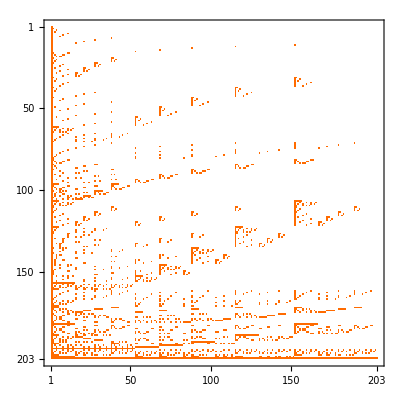

```mathematica
Table[gen6Coeff[allGraphs6[k,"genfour"]],{k,allGraphs6AtomKeys}]//Inverse//MatrixPlot
```

```mathematica
allGraphs6[K6Key,"genfour"]
```

g1x2x3x4x5x6

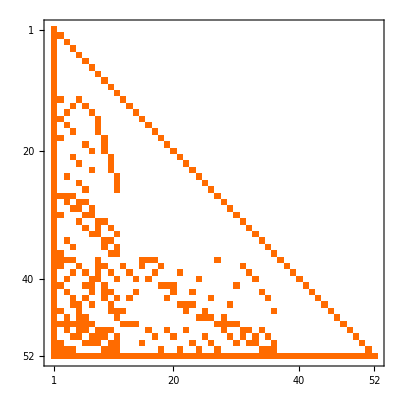

```mathematica
Table[full5Coeff[allGraphs5[k,"colofour"]],{k,gen5Sorted}]//MatrixPlot
```

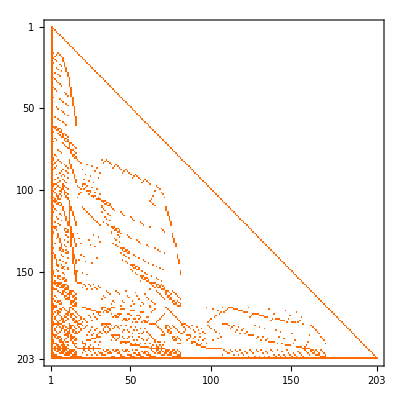

```mathematica
Table[full6Coeff[allGraphs6[k,"colofour"]],{k,gen6Sorted}]//MatrixPlot
```

```mathematica
otherOrder6=Table[gen6Symbols[[ U[[k]]]],{k,1,203}]
```

{g1x2x3x4x5x6,g1x2x3x4x56,g1x2x3x46x5,g1x2x3x45x6,g1x26x3x4x5,g1x23x4x5x6,g1x2x36x4x5,g13x2x4x56,g1x25x36x4,g1x23x45x6,g16x2x3x4x5,g156x24x3,g124x35x6,g14x23x56,g1x236x4x5,g15x23x4x6,g1x25x34x6,g1x24x3x5x6,g1x25x3x4x6,g13x2x45x6,g13x24x5x6,g13x2x46x5,g1x26x3x45,g1x26x35x4,g1x26x34x5,g1x24x36x5,g1x24x35x6,g1x24x3x56,g1x2x34x56,g1x23x4x56,g1x2x35x46,g16x2x345,g16x235x4,g16x234x5,g1234x5x6,g1x2346x5,g1x2x3456,g124x36x5,g125x34x6,g125x3x46,g13x246x5,g126x35x4,g126x3x45,g14x25x36,g15x23x46,g14x26x35,g1x234x56,g16x24x35,g15x26x34,g1x245x3x6,g1x256x3x4,g1x246x3x5,g136x2x4x5,g126x3x4x5,g124x3x5x6,g16x2x34x5,g16x2x3x45,g16x25x3x4,g1x2x345x6,g16x24x3x5,g16x2x35x4,g15x2x3x4x6,g1x2x346x5,g15x2x3x46,g123x4x5x6,g1x234x5x6,g1x235x4x6,g134x2x5x6,g1x2x356x4,g135x2x4x6,g1x2x34x5x6,g13x2456,g145x236,g123x456,g1256x3x4,g145x26x3,g136x25x4,g135x2x46,g12x345x6,g1x246x35,g12x35x46,g1235x4x6,g1x2356x4,g1x2345x6,g13x256x4,g13x2x456,g126x34x5,g1x235x46,g16x25x34,g16x23x45,g145x2x3x6,g15x24x36,g156x2x34,g14x2x3x56,g14x2x36x5,g134x25x6,g124x3x56,g13x26x45,g1x24x356,g1x236x45,g15x2x36x4,g136x24x5,g14x256x3,g1x256x34,g1x23x456,g123x46x5,g16x245x3,g1245x3x6,g1236x4x5,g1x2456x3,g1345x26,g1356x24,g1346x25,g146x235,g12x3456,g156x234,g124x356,g126x345,g125x346,g1345x2x6,g1356x2x4,g1346x2x5,g134x26x5,g15x2x34x6,g134x2x56,g13x245x6,g146x2x35,g146x25x3,g146x23x5,g14x2x356,g14x236x5,g14x235x6,g135x24x6,g136x2x45,g135x26x4,g145x2x36,g14x2x3x5x6,g146x2x3x5,g145x23x6,g156x23x4,g15x2x346,g12x356x4,g12x3x456,g12x346x5,g15x236x4,g15x234x6,g14x26x3x5,g1x2x36x45,g12x3x46x5,g12x36x45,g156x2x3x4,g12x3x4x56,g12x36x4x5,g14x25x3x6,g1x2x3x456,g12x34x5x6,g12x3x4x5x6,g12x35x4x6,g12x34x56,g1x245x36,g14x2x35x6,g12346x5,g16x2345,g1456x23,g1245x36,g1235x46,g135x246,g13x26x4x5,g125x3x4x6,g1456x2x3,g14x23x5x6,g14x2356,g1234x56,g134x256,g125x36x4,g1x25x3x46,g13x2x4x5x6,g15x26x3x4,g123x45x6,g123x4x56,g1x26x345,g1246x3x5,g12356x4,g1x23456,g15x2346,g1246x35,g1236x45,g136x245,g16x23x4x5,g1x25x346,g1256x34,g13x25x4x6,g1x2x35x4x6,g13x25x46,g12x3x45x6,g13x24x56,g15x24x3x6,g13456x2,g12456x3,g12345x6,g1x23x46x5,g15x246x3,g123456}

```mathematica
ordergen6Coeff[form_]:=Table[Coefficient[form,term],{term, otherOrder6}]
```

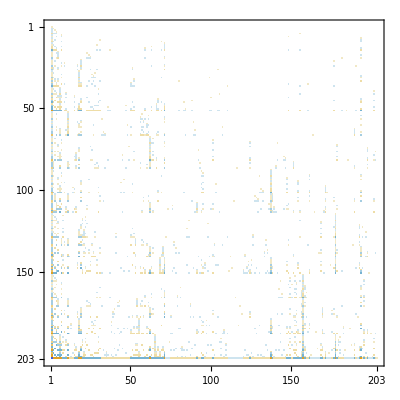

```mathematica
Table[ordergen6Coeff[allGraphs6[k,"genfour"]],{k,allGraphs6AtomKeys}]//MatrixPlot
```

```mathematica
RandomSample[Keys[allGraphs6],10]
```

{12495342,7151494,62086,6406478,2152290,6995757,8821282,4812129,36030,4864701}

```mathematica
gen6Coeff[allGraphs6[1674144,"genfour"]]
```

{2,0,0,0,0,0,0,0,-1,-1,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[full6Coeff[allGraphs6[k,"colofour"]],{k,gen6Sorted}].gen6Coeff[allGraphs6[1674144,"genfour"]]
```

{2,2,2,2,2,2,2,2,1,1,2,1,2,1,1,2,2,2,2,2,2,2,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,2,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,1,1,2,2,2,2,1,1,2,0,1,1,1,-1,-1,1,1,1,2,0,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,2,1,1,2,1,0,1,1,1,2,1,1,1,1,1,1,1,0,-1,-1,0,-1,-1,1,1,1,2,0,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,2,1,1,0,2,0,1,1,0,-1,-1,1,-1,-1,-1,0,1,1,0,1,0,0,1,1,1,0,0,1,1,1,0,0,1,-1,-1,-1,0,0,1,1,1,0,1,0,0,-1,-1,-1,1,0,1}

```mathematica
Monitor[Table[Length[allGraphs6[k,"genfour"]],{k,Keys[allGraphs6]}],k]//Tally//Sort
```

{{0,203},{2,225},{3,1980},{4,840},{5,2170},{6,711},{7,1140},{8,975},{9,4140},{10,1965},{11,2442},{12,2940},{13,2220},{14,2655},{15,2340},{16,2440},{17,495},{18,1890},{19,360},{20,2310},{21,1035},{22,945},{23,720},{24,1110},{25,310},{26,915},{27,360},{28,825},{29,480},{30,825},{31,840},{32,540},{33,600},{34,825},{35,350},{36,900},{37,660},{38,60},{39,180},{40,180},{41,900},{42,600},{43,450},{45,240},{46,405},{47,180},{48,150},{49,360},{50,180},{51,162},{52,51},{53,240},{55,15},{58,45},{59,60},{60,240},{61,180},{63,210},{65,180},{67,90},{70,225},{72,60},{77,20},{87,60},{89,15},{92,180},{107,45},{109,60},{114,60},{131,90},{151,15},{152,15},{189,65},{199,90},{202,31},{203,1}}

```mathematica
RandomSample[Select[Keys[allGraphs6],Length[allGraphs6[#,"genfour"]]==11&],10]
```

{730570,5513458,6574243,6918223,6384208,5501142,796096,5375920,5044303,6580722}

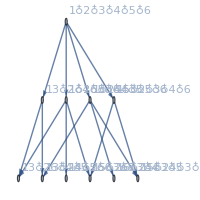

```mathematica
FormulaGraph[allGraphs6[4805203,"genfour"]]
```

```mathematica
Table[allGraphs6[k,"genfour"],{k,{0,K6Key,K5Key}}]
```

{g123456,g1x2x3x4x5x6,g12x3x4x5x6+g13x2x4x5x6+g14x2x3x5x6+g15x2x3x4x6+g16x2x3x4x5-4 g1x2x3x4x5x6}

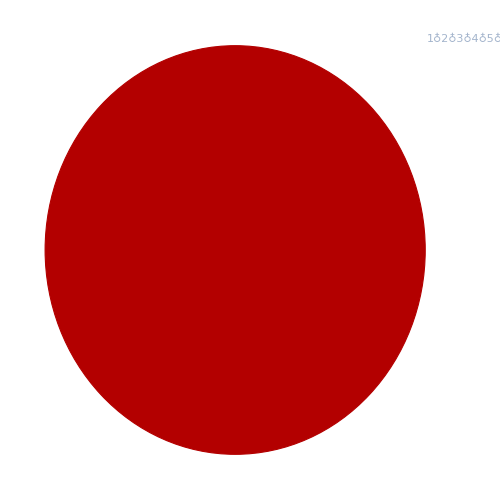
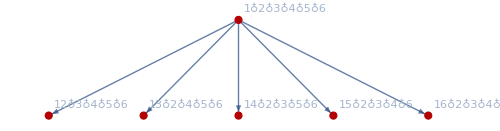
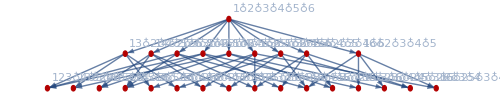
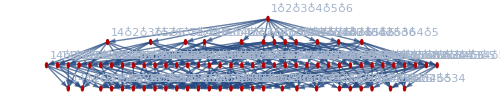

```mathematica
Table[Graph[FormulaGraph[allGraphs6[k,"colofour"]],GraphHighlight->VertexList[FormulaGraph[allGraphs6[k,"genfour"]]],ImageSize->500],{k,{K6Key,K5Key,K4Key,K3Key}}]
```

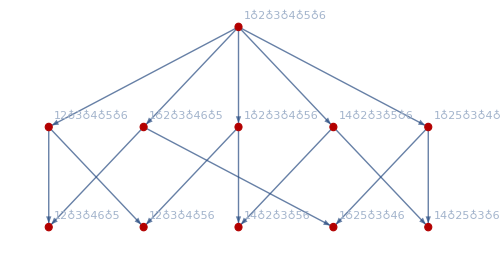
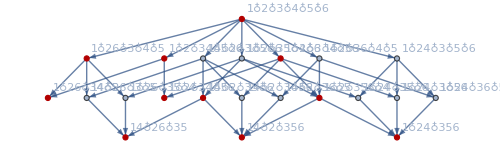
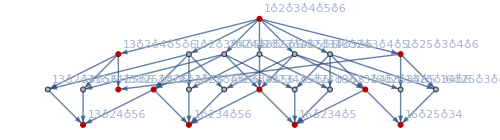
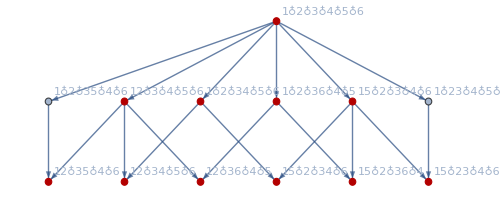
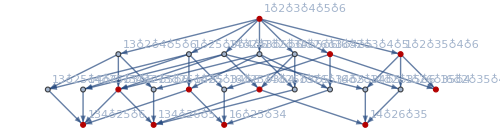
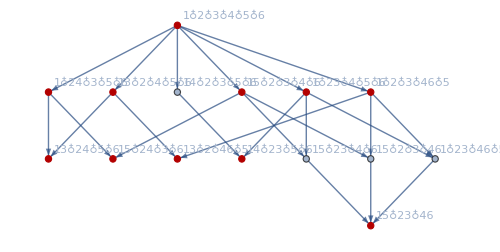
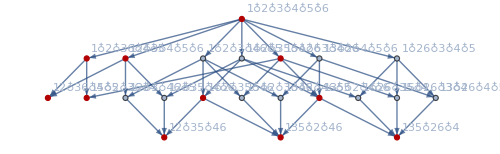
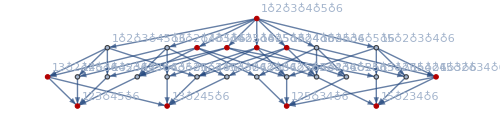

```mathematica
Table[Graph[FormulaGraph[allGraphs6[k,"colofour"]],GraphHighlight->VertexList[FormulaGraph[allGraphs6[k,"genfour"]]],ImageSize->500],{k,RandomSample[Select[Keys[allGraphs6],Length[allGraphs6[#,"genfour"]]==11&],10]}]
```